```mathematica
s0 = ({{1, 0}, {0, 1}});
sx = ({{0, 1}, {1, 0}});
sy = ({{0, -ⅈ}, {ⅈ, 0}});
sz=({{1, 0}, {0, -1}});
```

```mathematica
I0[L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];
```

```mathematica
X[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=sx;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];

Y[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=sy;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];

Z[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=sz;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];
```

```mathematica
Rzx[i_,j_,ϕ_]:=Cos[ϕ]I0[3]+ⅈ Sin[ϕ]Z[i,3].X[j,3];
```

```mathematica
Cos[ϕ]Cos[θ]I0[3]+ⅈ Sin[θ]Sin[ϕ]Z[1,3].Y[2,3].X[3,3]+ⅈ Cos[θ]Sin[ϕ]Z[1,3].X[2,3]+ⅈ Cos[ϕ]Sin[θ]Z[2,3].X[3,3]-Rzx[1,2,ϕ].Rzx[2,3,θ]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Rm[a_,b_,c_,d_]:= a I0[3] + ⅈ b Z[1,3].Y[2,3].X[3,3]+ⅈ c Z[1,3].X[2,3]+ⅈ d Z[2,3].X[3,3]
```

```mathematica
Rm[Cos[ϕ]Cos[θ],Sin[θ]Sin[ϕ],Cos[θ]Sin[ϕ],Cos[ϕ]Sin[θ]]-Rzx[1,2,ϕ].Rzx[2,3,θ]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Rm[a_,b_,c_,d_]:= a I0[3] + ⅈ b Z[1,3].Y[2,3].X[3,3]+ⅈ c Z[1,3].X[2,3]+ⅈ d Z[2,3].X[3,3]
```

```mathematica
a Z[1,3].X[2,3]- b Z[2,3].X[3,3]+ⅈ c I0[3]+d Z[1,3].Y[2,3].X[3,3]-Z[1,3].X[2,3].Rm[a,b,c,d]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
(Cos[ϕ]I0[3]+ⅈ Sin[ϕ]Z[1,3].X[2,3]).(Cos[θ]I0[3]+ⅈ Sin[θ]Z[2,3].X[3,3]).(Cos[λ]I0[3]+ⅈ Sin[λ]Z[1,3].X[2,3]).(Cos[τ]I0[3]+ⅈ Sin[τ]Z[2,3].X[3,3]) - Rzx[1,2,ϕ].Rzx[2,3,θ].Rzx[1,2,λ].Rzx[2,3,τ]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Simplify[(Cos[ϕ]I0[3]+ⅈ Sin[ϕ]Z[1,3].X[2,3]).(Cos[τ]Cos[λ]Cos[θ]I0[3]+ⅈ Cos[τ]Cos[λ]Sin[θ]Z[2,3].X[3,3]+ⅈ Sin[τ]Cos[λ]Cos[θ]Z[2,3].X[3,3]-Sin[τ]Cos[λ]Sin[θ]I0[3]+ⅈ Cos[τ] Sin[λ]Cos[θ]Z[1,3].X[2,3]- ⅈ Cos[τ] Sin[λ] Sin[θ]Z[1,3].Y[2,3].X[3,3]- Sin[τ] Sin[λ]Cos[θ]Z[1,3].X[2,3].Z[2,3].X[3,3]- Sin[τ] Sin[λ] Sin[θ]Z[2,3].Z[1,3].Y[2,3] )- Rzx[1,2,ϕ].Rzx[2,3,θ].Rzx[1,2,λ].Rzx[2,3,τ]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Simplify[((Cos[τ]Cos[λ]Cos[θ]Cos[ϕ]I0[3]+ⅈ Cos[τ]Cos[λ]Cos[θ]Sin[ϕ]Z[1,3].X[2,3])+ⅈ Cos[τ]Cos[λ]Sin[θ](Cos[ϕ]I0[3]+ⅈ Sin[ϕ]Z[1,3].X[2,3]).Z[2,3].X[3,3]+ⅈ Sin[τ]Cos[λ]Cos[θ](Cos[ϕ]I0[3]+ⅈ Sin[ϕ]Z[1,3].X[2,3]).Z[2,3].X[3,3]-Sin[τ]Cos[λ]Sin[θ](Cos[ϕ]I0[3]+ⅈ Sin[ϕ]Z[1,3].X[2,3]).I0[3]+ⅈ Cos[τ] Sin[λ]Cos[θ](Cos[ϕ]I0[3]+ⅈ Sin[ϕ]Z[1,3].X[2,3]).Z[1,3].X[2,3]- ⅈ Cos[τ] Sin[λ] Sin[θ](Cos[ϕ]I0[3]+ⅈ Sin[ϕ]Z[1,3].X[2,3]).Z[1,3].Y[2,3].X[3,3]- Sin[τ] Sin[λ]Cos[θ](Cos[ϕ]I0[3]+ⅈ Sin[ϕ]Z[1,3].X[2,3]).Z[1,3].X[2,3].Z[2,3].X[3,3]- Sin[τ] Sin[λ] Sin[θ](Cos[ϕ]I0[3]+ⅈ Sin[ϕ]Z[1,3].X[2,3]).Z[2,3].Z[1,3].Y[2,3] )- Rzx[1,2,ϕ].Rzx[2,3,θ].Rzx[1,2,λ].Rzx[2,3,τ]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Simplify[((Cos[τ]Cos[λ]Cos[θ]Cos[ϕ]I0[3]+ⅈ Cos[τ]Cos[λ]Cos[θ]Sin[ϕ]Z[1,3].X[2,3])+(ⅈ Cos[τ]Cos[λ]Sin[θ]Cos[ϕ]Z[2,3].X[3,3]+ⅈ Cos[τ]Cos[λ]Sin[θ] Sin[ϕ]Z[1,3].Y[2,3].X[3,3])+(ⅈ Sin[τ]Cos[λ]Cos[θ]Cos[ϕ]Z[2,3].X[3,3]+ⅈ Sin[τ]Cos[λ]Cos[θ]Sin[ϕ]Z[1,3].Y[2,3].X[3,3])+(-Sin[τ]Cos[λ]Sin[θ]Cos[ϕ]I0[3]-ⅈ Sin[τ]Cos[λ]Sin[θ]Sin[ϕ]Z[1,3].X[2,3])+(ⅈ Cos[τ] Sin[λ]Cos[θ]Cos[ϕ]I0[3].Z[1,3].X[2,3]-Cos[τ] Sin[λ]Cos[θ]Sin[ϕ]I0[3])+(- ⅈ Cos[τ] Sin[λ] Sin[θ]Cos[ϕ]Z[1,3].Y[2,3].X[3,3]+ⅈ Cos[τ] Sin[λ] Sin[θ] Sin[ϕ]Z[2,3].X[3,3])+(ⅈ Sin[τ] Sin[λ]Cos[θ]Cos[ϕ]Z[1,3].Y[2,3].X[3,3]-ⅈ Sin[τ] Sin[λ]Cos[θ]Sin[ϕ]Z[2,3].X[3,3])+(- Sin[τ] Sin[λ] Sin[θ]Cos[ϕ]Z[2,3].Z[1,3].Y[2,3]+ⅈ  Sin[τ] Sin[λ] Sin[θ]ⅈ Sin[ϕ]I0[3]) )- Rzx[1,2,ϕ].Rzx[2,3,θ].Rzx[1,2,λ].Rzx[2,3,τ]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Simplify[(Cos[τ]Cos[λ]Cos[θ]Cos[ϕ]-Sin[τ]Cos[λ]Sin[θ]Cos[ϕ]+ⅈ  Sin[τ] Sin[λ] Sin[θ]ⅈ Sin[ϕ] -Cos[τ] Sin[λ]Cos[θ]Sin[ϕ])I0[3]+(ⅈ Cos[τ]Cos[λ]Cos[θ]Sin[ϕ]-ⅈ Sin[τ]Cos[λ]Sin[θ]Sin[ϕ]+ⅈ Cos[τ] Sin[λ]Cos[θ]Cos[ϕ]+ⅈ Sin[τ] Sin[λ] Sin[θ]Cos[ϕ])Z[1,3].X[2,3]+(ⅈ Cos[τ]Cos[λ]Sin[θ]Cos[ϕ]+ⅈ Sin[τ]Cos[λ]Cos[θ]Cos[ϕ]+ⅈ Cos[τ] Sin[λ] Sin[θ] Sin[ϕ]-ⅈ Sin[τ] Sin[λ]Cos[θ]Sin[ϕ])Z[2,3].X[3,3]+(ⅈ Cos[τ]Cos[λ]Sin[θ] Sin[ϕ]+ⅈ Sin[τ]Cos[λ]Cos[θ]Sin[ϕ]+- ⅈ Cos[τ] Sin[λ] Sin[θ]Cos[ϕ]+ⅈ Sin[τ] Sin[λ]Cos[θ]Cos[ϕ])Z[1,3].Y[2,3].X[3,3]- Rzx[1,2,ϕ].Rzx[2,3,θ].Rzx[1,2,λ].Rzx[2,3,τ]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Clear[θ,ϕ,λ,τ]

(Cos[τ]Cos[λ]Cos[θ]Cos[ϕ]-Sin[τ]Cos[λ]Sin[θ]Cos[ϕ]+ⅈ  Sin[τ] Sin[λ] Sin[θ]ⅈ Sin[ϕ] -Cos[τ] Sin[λ]Cos[θ]Sin[ϕ])

(ⅈ Cos[τ]Cos[λ]Cos[θ]Sin[ϕ]-ⅈ Sin[τ]Cos[λ]Sin[θ]Sin[ϕ]+ⅈ Cos[τ] Sin[λ]Cos[θ]Cos[ϕ]+ⅈ Sin[τ] Sin[λ] Sin[θ]Cos[ϕ])

(ⅈ Cos[τ]Cos[λ]Sin[θ]Cos[ϕ]+ⅈ Sin[τ]Cos[λ]Cos[θ]Cos[ϕ]+ⅈ Cos[τ] Sin[λ] Sin[θ] Sin[ϕ]-ⅈ Sin[τ] Sin[λ]Cos[θ]Sin[ϕ])

(ⅈ Cos[τ]Cos[λ]Sin[θ] Sin[ϕ]+ⅈ Sin[τ]Cos[λ]Cos[θ]Sin[ϕ]+- ⅈ Cos[τ] Sin[λ] Sin[θ]Cos[ϕ]+ⅈ Sin[τ] Sin[λ]Cos[θ]Cos[ϕ])
```

Cos[θ] Cos[λ] Cos[τ] Cos[ϕ]-Cos[λ] Cos[ϕ] Sin[θ] Sin[τ]-Cos[θ] Cos[τ] Sin[λ] Sin[ϕ]-Sin[θ] Sin[λ] Sin[τ] Sin[ϕ]

ⅈ Cos[θ] Cos[τ] Cos[ϕ] Sin[λ]+ⅈ Cos[ϕ] Sin[θ] Sin[λ] Sin[τ]+ⅈ Cos[θ] Cos[λ] Cos[τ] Sin[ϕ]-ⅈ Cos[λ] Sin[θ] Sin[τ] Sin[ϕ]

ⅈ Cos[λ] Cos[τ] Cos[ϕ] Sin[θ]+ⅈ Cos[θ] Cos[λ] Cos[ϕ] Sin[τ]+ⅈ Cos[τ] Sin[θ] Sin[λ] Sin[ϕ]-ⅈ Cos[θ] Sin[λ] Sin[τ] Sin[ϕ]

-ⅈ Cos[τ] Cos[ϕ] Sin[θ] Sin[λ]+ⅈ Cos[θ] Cos[ϕ] Sin[λ] Sin[τ]+ⅈ Cos[λ] Cos[τ] Sin[θ] Sin[ϕ]+ⅈ Cos[θ] Cos[λ] Sin[τ] Sin[ϕ]

```mathematica
a[θ_,ϕ_,λ_,τ_]:=(Cos[τ]Cos[λ]Cos[θ]Cos[ϕ]-Sin[τ]Cos[λ]Sin[θ]Cos[ϕ]-  Sin[τ] Sin[λ] Sin[θ]Sin[ϕ] -Cos[τ] Sin[λ]Cos[θ]Sin[ϕ]);
b[θ_,ϕ_,λ_,τ_]:=(Cos[τ]Cos[λ]Cos[θ]Sin[ϕ]- Sin[τ]Cos[λ]Sin[θ]Sin[ϕ]+ Cos[τ] Sin[λ]Cos[θ]Cos[ϕ]+ Sin[τ] Sin[λ] Sin[θ]Cos[ϕ]);
c[θ_,ϕ_,λ_,τ_]:=( Cos[τ]Cos[λ]Sin[θ]Cos[ϕ]+ Sin[τ]Cos[λ]Cos[θ]Cos[ϕ]+ Cos[τ] Sin[λ] Sin[θ] Sin[ϕ]- Sin[τ] Sin[λ]Cos[θ]Sin[ϕ]);
d[θ_,ϕ_,λ_,τ_]:=( Cos[τ]Cos[λ]Sin[θ] Sin[ϕ]+ Sin[τ]Cos[λ]Cos[θ]Sin[ϕ]+-  Cos[τ] Sin[λ] Sin[θ]Cos[ϕ]+Sin[τ] Sin[λ]Cos[θ]Cos[ϕ]);
```

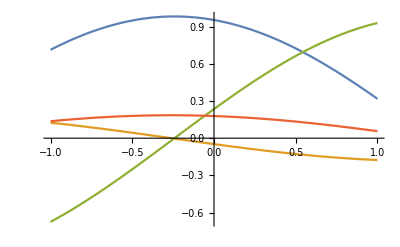

```mathematica
θ=0.3;
ϕ=0.3;
λ=-0.35;
Plot[{a[θ,ϕ,λ,τ],b[θ,ϕ,λ,τ],c[θ,ϕ,λ,τ],d[θ,ϕ,λ,τ]},{τ,-1,1}]
```

```mathematica
ϕ=0.2;
λ=-0.35;
Plot3D[{b[θ,ϕ,λ,τ],c[θ,ϕ,λ,τ],0},{τ,-1,1},{θ,-1,1}]
```

-Graphics3D-

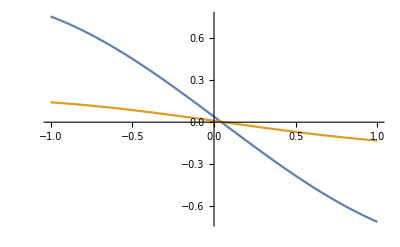

```mathematica
θ=0.3;
ϕ=θ;
τ = 0.06;
Plot[{b[θ,ϕ,-θ-λ,-θ+τ],c[θ,ϕ,-θ-λ,-θ+τ]},{λ,-1,1}]
```

```mathematica
θ=0.3;
ϕ=θ;
Plot3D[{b[θ,ϕ,-θ-λ,-θ+τ],c[θ,ϕ,-θ-λ,-θ+τ],0},{τ,-1,1},{λ,-1,1}]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[{b[θ,θ,-θ-λ,-θ+τ],c[θ,θ,-θ-λ,-θ+τ],0},{τ,-π,π},{λ,-π,π}],{θ,0,π,0.01}]
```

```mathematica
Clear[θ,ϕ,λ,τ]
a[θ,θ,-θ-λ,-θ+τ]
b[θ,θ,-θ-λ,-θ+τ]
c[θ,θ,-θ-λ,-θ+τ]
d[θ,θ,-θ-λ,-θ+τ]
```

Cos[θ]^2 Cos[θ+λ] Cos[θ-τ]+Cos[θ] Cos[θ-τ] Sin[θ] Sin[θ+λ]+Cos[θ] Cos[θ+λ] Sin[θ] Sin[θ-τ]-Sin[θ]^2 Sin[θ+λ] Sin[θ-τ]

Cos[θ] Cos[θ+λ] Cos[θ-τ] Sin[θ]-Cos[θ]^2 Cos[θ-τ] Sin[θ+λ]+Cos[θ+λ] Sin[θ]^2 Sin[θ-τ]+Cos[θ] Sin[θ] Sin[θ+λ] Sin[θ-τ]

Cos[θ] Cos[θ+λ] Cos[θ-τ] Sin[θ]-Cos[θ-τ] Sin[θ]^2 Sin[θ+λ]-Cos[θ]^2 Cos[θ+λ] Sin[θ-τ]-Cos[θ] Sin[θ] Sin[θ+λ] Sin[θ-τ]

Cos[θ+λ] Cos[θ-τ] Sin[θ]^2+Cos[θ] Cos[θ-τ] Sin[θ] Sin[θ+λ]-Cos[θ] Cos[θ+λ] Sin[θ] Sin[θ-τ]+Cos[θ]^2 Sin[θ+λ] Sin[θ-τ]

```mathematica
θ=0.301;
minV = NMinimize[{b[θ,θ,-θ-λ,-θ+τ]^2+c[θ,θ,-θ-λ,-θ+τ]^2,-θ<λ<θ,-θ<τ<θ},{λ,τ},AccuracyGoal->8];
λV = λ/.minV[[2,1]];
τV = τ/.minV[[2,2]];
```

```mathematica
a[θ,θ,-θ-λV,-θ+τV]
b[θ,θ,-θ-λV,-θ+τV]
c[θ,θ,-θ-λV,-θ+τV]
d[θ,θ,-θ-λV,-θ+τV]
```

0.982838

2.22045×10^-16

1.38778×10^-16

0.184469

```mathematica
V[θ_]:=Block[{λV,τV,minV},
minV = NMinimize[{b[θ,θ,-θ-λ,-θ+τ]^2+c[θ,θ,-θ-λ,-θ+τ]^2,-θ<λ<θ,-θ<τ<θ},{λ,τ},AccuracyGoal->8];
λV = λ/.minV[[2,1]];
τV = τ/.minV[[2,2]];
 {λV,τV}
];
```

```mathematica
θ0=0.001;
dθ=0.01;
λVl = Table[{θ,V[θ][[1]]},{θ,θ0,0.5,dθ}];
τVl = Table[{θ,V[θ][[2]]},{θ,θ0,0.5,dθ}];
```

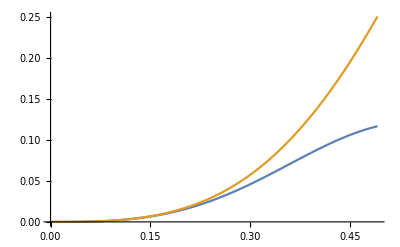

```mathematica
ListPlot[{λVl,τVl},Joined->True]
```

```mathematica
λVl
```

{{0.001,2.×10^-9},{0.011,2.6629×10^-6},{0.021,0.0000185063},{0.031,0.0000595252},{0.041,0.000137607},{0.051,0.000264595},{0.061,0.000452225},{0.071,0.000712068},{0.081,0.00105556},{0.091,0.00149388},{0.101,0.00203795},{0.111,0.0026984},{0.121,0.00348548},{0.131,0.00440898},{0.141,0.00547818},{0.151,0.00670181},{0.161,0.00808785},{0.171,0.00964352},{0.181,0.0113752},{0.191,0.0132881},{0.201,0.0153866},{0.211,0.0176736},{0.221,0.0201506},{0.231,0.0228179},{0.241,0.0256738},{0.251,0.0287151},{0.261,0.0319368},{0.271,0.0353317},{0.281,0.0388908},{0.291,0.042603},{0.301,0.0464549},{0.311,0.0504314},{0.321,0.0545148},{0.331,0.0586859},{0.341,0.0629234},{0.351,0.0672044},{0.361,0.0715042},{0.371,0.0757971},{0.381,0.0800563},{0.391,0.0842541},{0.401,0.0883624},{0.411,0.0923529},{0.421,0.0961976},{0.431,0.0998687},{0.441,0.103339},{0.451,0.106583},{0.461,0.109576},{0.471,0.112295},{0.481,0.114717},{0.491,0.116822}}

```mathematica
τVl
```

{{0.001,2.×10^-9},{0.011,2.66262×10^-6},{0.021,0.0000185227},{0.031,0.0000596317},{0.041,0.000138073},{0.051,0.00026598},{0.061,0.000455637},{0.071,0.000719381},{0.081,0.00106975},{0.091,0.00151938},{0.101,0.00208112},{0.111,0.00276799},{0.121,0.00359318},{0.131,0.00457015},{0.141,0.00571254},{0.151,0.00703417},{0.161,0.00854909},{0.171,0.0102716},{0.181,0.012216},{0.191,0.014397},{0.201,0.0168293},{0.211,0.0195276},{0.221,0.0225069},{0.231,0.0257819},{0.241,0.0293675},{0.251,0.0332782},{0.261,0.0375284},{0.271,0.0421322},{0.281,0.0471032},{0.291,0.0524547},{0.301,0.0581992},{0.311,0.0643484},{0.321,0.0709134},{0.331,0.0779042},{0.341,0.0853297},{0.351,0.0931977},{0.361,0.101515},{0.371,0.110287},{0.381,0.119517},{0.391,0.129207},{0.401,0.13936},{0.411,0.149973},{0.421,0.161046},{0.431,0.172575},{0.441,0.184555},{0.451,0.19698},{0.461,0.209843},{0.471,0.223134},{0.481,0.236845},{0.491,0.250964}}

```mathematica
al = Table[{(θi-1)*dθ+θ0,a[(θi-1)*dθ+θ0,(θi-1)*dθ+θ0,-(θi-1)*dθ-θ0-λVl[[θi,2]],-(θi-1)*dθ-θ0+τVl[[θi,2]]]},{θi,1,Length[λVl]}];
bl = Table[{(θi-1)*dθ+θ0,b[(θi-1)*dθ+θ0,(θi-1)*dθ+θ0,-(θi-1)*dθ-θ0-λVl[[θi,2]],-(θi-1)*dθ-θ0+τVl[[θi,2]]]},{θi,1,Length[λVl]}];
cl = Table[{(θi-1)*dθ+θ0,c[(θi-1)*dθ+θ0,(θi-1)*dθ+θ0,-(θi-1)*dθ-θ0-λVl[[θi,2]],-(θi-1)*dθ-θ0+τVl[[θi,2]]]},{θi,1,Length[λVl]}];
dl = Table[{(θi-1)*dθ+θ0,d[(θi-1)*dθ+θ0,(θi-1)*dθ+θ0,-(θi-1)*dθ-θ0-λVl[[θi,2]],-(θi-1)*dθ-θ0+τVl[[θi,2]]]},{θi,1,Length[λVl]}];
```

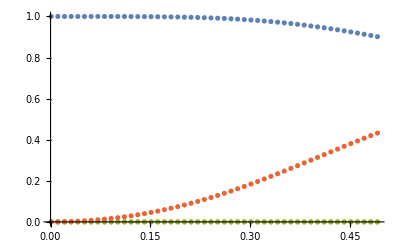

```mathematica
ListPlot[{al,bl,cl,dl}]
```

```mathematica
cosl = Table[{(θi-1)*dθ+θ0,Cos[(θi-1)*dθ+θ0]},{θi,1,Length[λVl]}];
sinl = Table[{(θi-1)*dθ+θ0,Sin[(θi-1)*dθ+θ0]},{θi,1,Length[λVl]}];
```

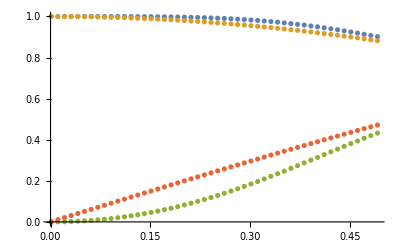

```mathematica
ListPlot[{al,cosl,dl,sinl}]
```

```mathematica
Clear[θ,ϕ,λ,τ]
θi=20;
θ=θi*dθ+θ0;
ϕ=θ;
λ = -θ-λVl[[θi+1,2]];
τ = -θ +τVl[[θi+1,2]];
Max[Abs[Simplify[a[θ,ϕ,λ,τ]I0[3]+ⅈ d[θ,ϕ,λ,τ]Z[1,3].Y[2,3].X[3,3]- Rzx[1,2,ϕ].Rzx[2,3,θ].Rzx[1,2,λ].Rzx[2,3,τ]]]]
```

1.11022×10^-16

```mathematica
θλτl = Table[{λVl[[l,1]],λVl[[l,2]],τVl[[l,2]]},{l,1,Length[λVl]}];
```

```mathematica
Export["C:\\Users\\jsten\\Documents\\Reaserch\\Quantum Gates\\Three_Site_Rotation\\angles.txt",θλτl ]
```

C:\Users\jsten\Documents\Reaserch\Quantum Gates\Three_Site_Rotation\angles.txt